```mathematica
∫_0^1 Log[1+x^2]ⅆx
```

-2+π/2+Log[2]

```mathematica
∫_0^9 ArcTan[u]ⅆu
```

9 ArcTan[9]-Log[82]/2

```mathematica
Integrate[(3 x^2+5x-12)Cos[3x],x]
```

1/9 ((5+6 x) Cos[3 x]+(-38+15 x+9 x^2) Sin[3 x])

```mathematica
Integrate[1/(Sin[x]^2 Cos[x]^2),x]
```

-2 Cot[2 x]

```mathematica
∫_1^2 1/(x(1+x^5))ⅆx
```

1/5 Log[64/33]

```mathematica
∫_0^3 1/(a^2+u^2)ⅆu
```

ConditionalExpression[ArcTan[3/a]/a,Re[a]≠0||Im[a]>3||Im[a]<-3]

```mathematica
∫_a^b (t-a)^3(b-t)^2 ⅆt
```

1/60 (a-b)^6

```mathematica
Plot3D[1/60 (a-b)^6,{a,-8,8},{b,-8,8}]
```

-Graphics3D-

```mathematica
Integrate[Cosh[x]/Sinh[x]^4,x]
```

-1/3 Csch[x]^3

```mathematica
lim_(x->0) Cos[x]
```

1

```mathematica
∫_(√2)^(√3) Sin[x]/(Sin[x]+Cos[x])ⅆx
```

1/2 (-√2+√3+Log[Cos[√2]+Sin[√2]]-Log[Cos[√3]+Sin[√3]])

```mathematica
Simplify[∫_(√2)^(√3) Sin[x]/(Sin[x]+Cos[x])ⅆx]
```

1/2 (-√2+√3+Log[Cos[√2]+Sin[√2]]-Log[Cos[√3]+Sin[√3]])

```mathematica
N[-π/4]
N[-π/4+π]
```

-0.785398

2.35619

```mathematica
N[√3]
```

1.73205

```mathematica
N[Log[2]]
```

0.693147

```mathematica
N[Log[3]]
```

1.09861

```mathematica
∫_(√2)^(√3) Cos[x]/(Sin[x]+Cos[x])ⅆx
```

1/2 (-√2+√3-Log[Cos[√2]+Sin[√2]]+Log[Cos[√3]+Sin[√3]])

```mathematica
∫_0^5 1/(1+x^2)ⅆx
```

ArcTan[5]

```mathematica
WolframAlpha["1/(1+(u^2/a^2))",IncludePods->{"Indefinite Integral"},PodStates->{"Step-by-step solution","Show all steps"}]
```

WolframAlphaQueryResults

```mathematica
(t-a)^3(b-t)^2
```

(b-t)^2 (-a+t)^3

```mathematica
Expand[(b-t)^2 (-a+t)^3]
```

-a^3 b^2+2 a^3 b t+3 a^2 b^2 t-a^3 t^2-6 a^2 b t^2-3 a b^2 t^2+3 a^2 t^3+6 a b t^3+b^2 t^3-3 a t^4-2 b t^4+t^5

```mathematica
Integrate[Expand[(b-t)^2 (-a+t)^3],t]
```

-a^3 b^2 t+a^3 b t^2+3/2 a^2 b^2 t^2-(a^3 t^3)/3-2 a^2 b t^3-a b^2 t^3+(3 a^2 t^4)/4+3/2 a b t^4+(b^2 t^4)/4-(3 a t^5)/5-(2 b t^5)/5+t^6/6

```mathematica
f[t_]:=-a^3 b^2 t+a^3 b t^2+3/2 a^2 b^2 t^2-(a^3 t^3)/3-2 a^2 b t^3-a b^2 t^3+(3 a^2 t^4)/4+3/2 a b t^4+(b^2 t^4)/4-(3 a t^5)/5-(2 b t^5)/5+t^6/6
```

```mathematica
f[b]-f[a]
```

a^6/60-(a^5 b)/10+(a^4 b^2)/4-(a^3 b^3)/3+(a^2 b^4)/4-(a b^5)/10+b^6/60

```mathematica
Simplify[%]
```

1/60 (a-b)^6

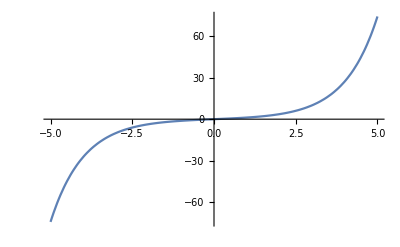

```mathematica
Plot[Sinh[x],{x,-5,5}]
```

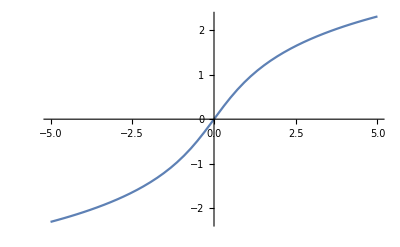

```mathematica
Plot[ArcSinh[x],{x,-5,5}]
```

```mathematica
Derivative[ArcSinh[x],x]
```

Derivative[ArcSinh[x],x]

```mathematica
∫_Sinh[0]^Sinh[9] Cosh[ArcSinh[u]]/(u^4 √(u^2+1))ⅆu
```

∫_0^Sinh[789] 1/u^4 ⅆu

```mathematica
WolframAlpha["1/(x(1+x^n))",IncludePods->{"Indefinite Integral"},PodStates->{"Step-by-step solution","Show all steps"}]
```

WolframAlphaQueryResults

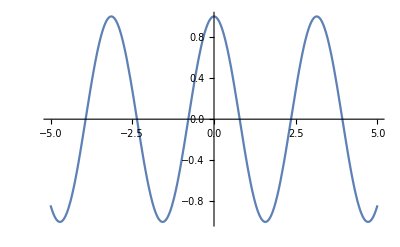

```mathematica
Plot[Cos[2x],{x,-5,5}]
```

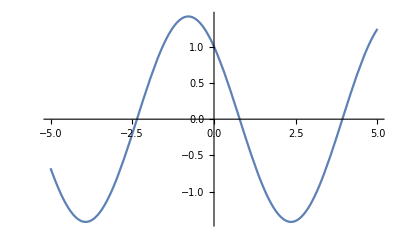

```mathematica
Plot[Cos[x]-Sin[x],{x,-5,5}]
```

```mathematica
Integrate[1/Sin[x],x]
```

-Log[Cos[x/2]]+Log[Sin[x/2]]

```mathematica
Integrate[1/Cos[x],x]
```

-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]

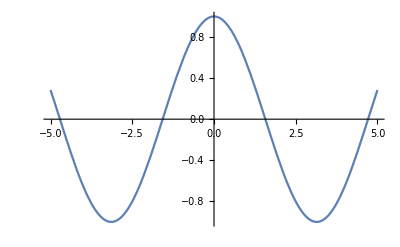

```mathematica
Plot[Cos[x],{x,-5,5}]
```

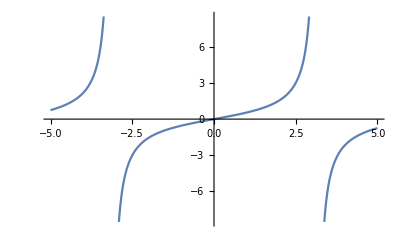

```mathematica
Plot[Tan[x/2],{x,-5,5}]
```

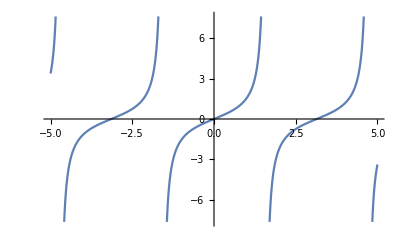

```mathematica
Plot[Tan[x],{x,-5,5}]
```

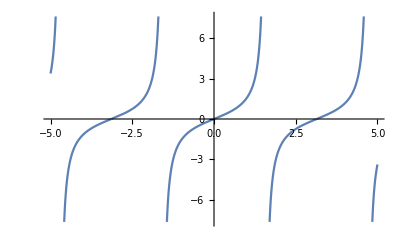

```mathematica
Plot[(2Tan[x/2])/(1-Tan[x/2]^2),{x,-5,5}]
```

```mathematica
Plot[Cos[x],{x,-5,5}]
```

-Graphics-

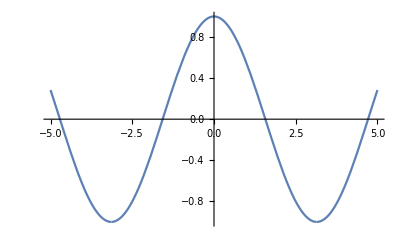

```mathematica
Plot[(1-Tan[x/2]^2)/(1+Tan[x/2]^2),{x,-5,5}]
```

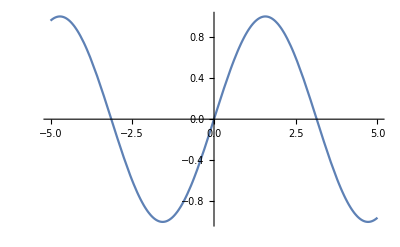

```mathematica
Plot[Sin[x],{x,-5,5}]
```

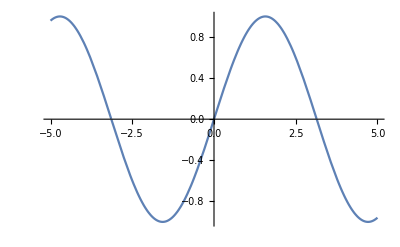

```mathematica
Plot[(2Tan[x/2])/(1+Tan[x/2]^2),{x,-5,5}]
```

```mathematica
WolframAlpha["1/cos(x)",IncludePods->{"Indefinite Integral"},PodStates->{"Step-by-step solution","Show all steps"}]
```

WolframAlphaQueryResults

```mathematica
Derivative[ArcSin[x],x]
```

Derivative[ArcSin[x],x]

```mathematica
∫_ⅇ^(√2) 1/Cos[x] ⅆx
```

∫_ⅇ^(√2) Sec[x]ⅆx

```mathematica
Integrate[Log[x],x]
```

-x+x Log[x]

```mathematica
Integrate[Log[1+x^2],x]
```

-2 x+2 ArcTan[x]+x Log[1+x^2]

```mathematica
Derivative[x*Log[1+x^2],x]
```

```mathematica
f[x_]:=x*Log[1+x^2]
```

```mathematica
D[f[x],x]
```

(2 x^2)/(1+x^2)+Log[1+x^2]

```mathematica
D[ArcTan[x],x]
```

1/(1+x^2)

```mathematica
Simplify[Integrate[Sin[3x]/3(6x+5),x]]
```

1/9 (-(5+6 x) Cos[3 x]+2 Sin[3 x])

```mathematica
Expand[Simplify[D[Sin[3x]/3(9 x^2+15x-38)+Cos[3x](2/3 x+5/9),x]]]
```

-112/3 Cos[3 x]+15 x Cos[3 x]+9 x^2 Cos[3 x]+10/3 Sin[3 x]+4 x Sin[3 x]

```mathematica
Simplify[D[Sin[3x]/3(9 x^2+15x-38),x]]
```

(-38+15 x+9 x^2) Cos[3 x]+(5+6 x) Sin[3 x]

```mathematica
Simplify[D[Cos[3x](2/3 x+5/9),x]]
```

2/3 Cos[3 x]-1/3 (5+6 x) Sin[3 x]

```mathematica
Simplify[D[-5/9 Cos[3 x]-2/3 x Cos[3 x]+2/9 Sin[3 x],x]]
```

1/3 (5+6 x) Sin[3 x]

```mathematica
Simplify[D[-1/3 (2x+5/3)Cos[3 x]+2/9 Sin[3 x],x]]
```

(5/3+2 x) Sin[3 x]

```mathematica
Simplify[D[Sin[3x]/3(3 x^2+11x-17),x]]
```

(-17+11 x+3 x^2) Cos[3 x]+1/3 (11+6 x) Sin[3 x]

```mathematica
Simplify[D[Sin[3x]/3(3 x^2+5x-12)+1/9((5+6x)Cos[3x]-2Sin[3x]),x]]
```

(-12+5 x+3 x^2) Cos[3 x]

```mathematica
Simplify[D[1/9(Sin[3x](9 x^2+15x-38)+Cos[3x](5+6x)),x]]
```

(-12+5 x+3 x^2) Cos[3 x]

```mathematica
Integrate[1/(Sin[x]^2 Cos[x]^2),x]
```

-2 Cot[2 x]

```mathematica
Integrate[1/Sin[x]^2,x]
```

-Cot[x]

```mathematica
Integrate[1/Cos[x]^2,x]
```

Tan[x]

```mathematica
D[-Cot[2x],x]
```

2 Csc[2 x]^2

```mathematica
D[-2Cot[2x],x]
```

4 Csc[2 x]^2

```mathematica
D[1/2(x-Log[Cos[x]+Sin[x]]),x]
```

1/2 (1-(Cos[x]-Sin[x])/(Cos[x]+Sin[x]))